# Complex Spacing Ratios: A Signature of Dissipative Quantum Chaos

## Goal: reproduce similar graphs to the ones in Fig. 1 from eq. (1)

## λ^NN: nearest neighbour eigenvalue? [?] λ^NNN: Next Nearest Neighbour eigenvalue [?]

## Genero con una distribución Poissoniana los elementos de matriz para generar la Fig 1.b?

```mathematica
wtf=RandomVariate[PoissonDistribution[#]]&/@ConstantArray[5,{10^4}];
```

```mathematica
ArrayReshape[wtf,{100,100}]//Eigenvalues
```

{Root499.Root[10795041836360029503977122726856756916109276587019849534047938463585333653305226762632788402453039307533018474842736-18294711282252192657999155808847302183085440949694935912245955091898887385715980864963271536385910508123750906472641 #1+4552217585632257305241802817841681499469011588316602777076149274617513939260933099934216253385765970021567593575731 #1^2+«147»+388422 #1^97-8023 #1^98-485 #1^99+#1^100&,8]499.45020117854176,Root21.9+7.68 ⅈRoot[10795041836360029503977122726856756916109276587019849534047938463585333653305226762632788402453039307533018474842736-18294711282252192657999155808847302183085440949694935912245955091898887385715980864963271536385910508123750906472641 #1+4552217585632257305241802817841681499469011588316602777076149274617513939260933099934216253385765970021567593575731 #1^2+«147»+388422 #1^97-8023 #1^98-485 #1^99+#1^100&,100]21.869126652592307,Root21.9-7.68 ⅈRoot[10795041836360029503977122726856756916109276587019849534047938463585333653305226762632788402453039307533018474842736-18294711282252192657999155808847302183085440949694935912245955091898887385715980864963271536385910508123750906472641 #1+4552217585632257305241802817841681499469011588316602777076149274617513939260933099934216253385765970021567593575731 #1^2+«147»+388422 #1^97-8023 #1^98-485 #1^99+#1^100&,99]21.869126652592307,Root-20.8+10.2 ⅈRoot[10795041836360029503977122726856756916109276587019849534047938463585333653305226762632788402453039307533018474842736-18294711282252192657999155808847302183085440949694935912245955091898887385715980864963271536385910508123750906472641 #1+4552217585632257305241802817841681499469011588316602777076149274617513939260933099934216253385765970021567593575731 #1^2+«147»+388422 #1^97-8023 #1^98-485 #1^99+#1^100&,12]-20.83002610963107,Root-20.8-10.2 ⅈRoot[10795041836360029503977122726856756916109276587019849534047938463585333653305226762632788402453039307533018474842736-18294711282252192657999155808847302183085440949694935912245955091898887385715980864963271536385910508123750906472641 #1+4552217585632257305241802817841681499469011588316602777076149274617513939260933099934216253385765970021567593575731 #1^2+«147»+388422 #1^97-8023 #1^98-485 #1^99+#1^100&,11]-20.83002610963107,Root-11.4+18.3 ⅈRoot[10795041836360029503977122726856756916109276587019849534047938463585333653305226762632788402453039307533018474842736-18294711282252192657999155808847302183085440949694935912245955091898887385715980864963271536385910508123750906472641 #1+4552217585632257305241802817841681499469011588316602777076149274617513939260933099934216253385765970021567593575731 #1^2+«147»+388422 #1^97-8023 #1^98-485 #1^99+#1^100&,28]-11.430622441092785,Root-11.4-18.3 ⅈRoot[10795041836360029503977122726856756916109276587019849534047938463585333653305226762632788402453039307533018474842736-18294711282252192657999155808847302183085440949694935912245955091898887385715980864963271536385910508123750906472641 #1+4552217585632257305241802817841681499469011588316602777076149274617513939260933099934216253385765970021567593575731 #1^2+«147»+388422 #1^97-8023 #1^98-485 #1^99+#1^100&,27]-11.430622441092785,Root-21.1+1.58 ⅈRoot[10795041836360029503977122726856756916109276587019849534047938463585333653305226762632788402453039307533018474842736-18294711282252192657999155808847302183085440949694935912245955091898887385715980864963271536385910508123750906472641 #1+4552217585632257305241802817841681499469011588316602777076149274617513939260933099934216253385765970021567593575731 #1^2+«147»+388422 #1^97-8023 #1^98-485 #1^99+#1^100&,10]-21.085659588923644,Root-21.1-1.58 ⅈRoot[10795041836360029503977122726856756916109276587019849534047938463585333653305226762632788402453039307533018474842736-18294711282252192657999155808847302183085440949694935912245955091898887385715980864963271536385910508123750906472641 #1+4552217585632257305241802817841681499469011588316602777076149274617513939260933099934216253385765970021567593575731 #1^2+«147»+388422 #1^97-8023 #1^98-485 #1^99+#1^100&,9]-21.085659588923644,Root-20.2+4.32 ⅈRoot[10795041836360029503977122726856756916109276587019849534047938463585333653305226762632788402453039307533018474842736-18294711282252192657999155808847302183085440949694935912245955091898887385715980864963271536385910508123750906472641 #1+4552217585632257305241802817841681499469011588316602777076149274617513939260933099934216253385765970021567593575731 #1^2+«147»+388422 #1^97-8023 #1^98-485 #1^99+#1^100&,14]-20.163134674719128,Root-20.2-4.32 ⅈRoot[10795041836360029503977122726856756916109276587019849534047938463585333653305226762632788402453039307533018474842736-18294711282252192657999155808847302183085440949694935912245955091898887385715980864963271536385910508123750906472641 #1+4552217585632257305241802817841681499469011588316602777076149274617513939260933099934216253385765970021567593575731 #1^2+«147»+388422 #1^97-8023 #1^98-485 #1^99+#1^100&,13]-20.163134674719128,Root-4.11+20.1 ⅈRoot[10795041836360029503977122726856756916109276587019849534047938463585333653305226762632788402453039307533018474842736-18294711282252192657999155808847302183085440949694935912245955091898887385715980864963271536385910508123750906472641 #1+4552217585632257305241802817841681499469011588316602777076149274617513939260933099934216253385765970021567593575731 #1^2+«147»+388422 #1^97-8023 #1^98-485 #1^99+#1^100&,44]-4.113973370024636,Root-4.11-20.1 ⅈRoot[10795041836360029503977122726856756916109276587019849534047938463585333653305226762632788402453039307533018474842736-18294711282252192657999155808847302183085440949694935912245955091898887385715980864963271536385910508123750906472641 #1+4552217585632257305241802817841681499469011588316602777076149274617513939260933099934216253385765970021567593575731 #1^2+«147»+388422 #1^97-8023 #1^98-485 #1^99+#1^100&,43]-4.113973370024636,Root17.8+9.73 ⅈRoot[10795041836360029503977122726856756916109276587019849534047938463585333653305226762632788402453039307533018474842736-18294711282252192657999155808847302183085440949694935912245955091898887385715980864963271536385910508123750906472641 #1+4552217585632257305241802817841681499469011588316602777076149274617513939260933099934216253385765970021567593575731 #1^2+«147»+388422 #1^97-8023 #1^98-485 #1^99+#1^100&,96]17.828883496996188,Root17.8-9.73 ⅈRoot[10795041836360029503977122726856756916109276587019849534047938463585333653305226762632788402453039307533018474842736-18294711282252192657999155808847302183085440949694935912245955091898887385715980864963271536385910508123750906472641 #1+4552217585632257305241802817841681499469011588316602777076149274617513939260933099934216253385765970021567593575731 #1^2+«147»+388422 #1^97-8023 #1^98-485 #1^99+#1^100&,95]17.828883496996188,Root13.2+15.2 ⅈRoot[10795041836360029503977122726856756916109276587019849534047938463585333653305226762632788402453039307533018474842736-18294711282252192657999155808847302183085440949694935912245955091898887385715980864963271536385910508123750906472641 #1+4552217585632257305241802817841681499469011588316602777076149274617513939260933099934216253385765970021567593575731 #1^2+«147»+388422 #1^97-8023 #1^98-485 #1^99+#1^100&,88]13.222977291122282,Root13.2-15.2 ⅈRoot[10795041836360029503977122726856756916109276587019849534047938463585333653305226762632788402453039307533018474842736-18294711282252192657999155808847302183085440949694935912245955091898887385715980864963271536385910508123750906472641 #1+4552217585632257305241802817841681499469011588316602777076149274617513939260933099934216253385765970021567593575731 #1^2+«147»+388422 #1^97-8023 #1^98-485 #1^99+#1^100&,87]13.222977291122282,Root16.7+11.1 ⅈRoot[10795041836360029503977122726856756916109276587019849534047938463585333653305226762632788402453039307533018474842736-18294711282252192657999155808847302183085440949694935912245955091898887385715980864963271536385910508123750906472641 #1+4552217585632257305241802817841681499469011588316602777076149274617513939260933099934216253385765970021567593575731 #1^2+«147»+388422 #1^97-8023 #1^98-485 #1^99+#1^100&,92]16.65803960765074,Root16.7-11.1 ⅈRoot[10795041836360029503977122726856756916109276587019849534047938463585333653305226762632788402453039307533018474842736-18294711282252192657999155808847302183085440949694935912245955091898887385715980864963271536385910508123750906472641 #1+4552217585632257305241802817841681499469011588316602777076149274617513939260933099934216253385765970021567593575731 #1^2+«147»+388422 #1^97-8023 #1^98-485 #1^99+#1^100&,91]16.65803960765074,Root-16.4+11.3 ⅈRoot[10795041836360029503977122726856756916109276587019849534047938463585333653305226762632788402453039307533018474842736-18294711282252192657999155808847302183085440949694935912245955091898887385715980864963271536385910508123750906472641 #1+4552217585632257305241802817841681499469011588316602777076149274617513939260933099934216253385765970021567593575731 #1^2+«147»+388422 #1^97-8023 #1^98-485 #1^99+#1^100&,18]-16.433668896949996,Root-16.4-11.3 ⅈRoot[10795041836360029503977122726856756916109276587019849534047938463585333653305226762632788402453039307533018474842736-18294711282252192657999155808847302183085440949694935912245955091898887385715980864963271536385910508123750906472641 #1+4552217585632257305241802817841681499469011588316602777076149274617513939260933099934216253385765970021567593575731 #1^2+«147»+388422 #1^97-8023 #1^98-485 #1^99+#1^100&,17]-16.433668896949996,Root-12.0+16.0 ⅈRoot[10795041836360029503977122726856756916109276587019849534047938463585333653305226762632788402453039307533018474842736-18294711282252192657999155808847302183085440949694935912245955091898887385715980864963271536385910508123750906472641 #1+4552217585632257305241802817841681499469011588316602777076149274617513939260933099934216253385765970021567593575731 #1^2+«147»+388422 #1^97-8023 #1^98-485 #1^99+#1^100&,24]-11.964324951032559,Root-12.0-16.0 ⅈRoot[10795041836360029503977122726856756916109276587019849534047938463585333653305226762632788402453039307533018474842736-18294711282252192657999155808847302183085440949694935912245955091898887385715980864963271536385910508123750906472641 #1+4552217585632257305241802817841681499469011588316602777076149274617513939260933099934216253385765970021567593575731 #1^2+«147»+388422 #1^97-8023 #1^98-485 #1^99+#1^100&,23]-11.964324951032559,Root-14.4+13.7 ⅈRoot[10795041836360029503977122726856756916109276587019849534047938463585333653305226762632788402453039307533018474842736-18294711282252192657999155808847302183085440949694935912245955091898887385715980864963271536385910508123750906472641 #1+4552217585632257305241802817841681499469011588316602777076149274617513939260933099934216253385765970021567593575731 #1^2+«147»+388422 #1^97-8023 #1^98-485 #1^99+#1^100&,20]-14.417803113033646,Root-14.4-13.7 ⅈRoot[10795041836360029503977122726856756916109276587019849534047938463585333653305226762632788402453039307533018474842736-18294711282252192657999155808847302183085440949694935912245955091898887385715980864963271536385910508123750906472641 #1+4552217585632257305241802817841681499469011588316602777076149274617513939260933099934216253385765970021567593575731 #1^2+«147»+388422 #1^97-8023 #1^98-485 #1^99+#1^100&,19]-14.417803113033646,Root8.69+17.9 ⅈRoot[10795041836360029503977122726856756916109276587019849534047938463585333653305226762632788402453039307533018474842736-18294711282252192657999155808847302183085440949694935912245955091898887385715980864963271536385910508123750906472641 #1+4552217585632257305241802817841681499469011588316602777076149274617513939260933099934216253385765970021567593575731 #1^2+«147»+388422 #1^97-8023 #1^98-485 #1^99+#1^100&,76]8.693295617909149,Root8.69-17.9 ⅈRoot[10795041836360029503977122726856756916109276587019849534047938463585333653305226762632788402453039307533018474842736-18294711282252192657999155808847302183085440949694935912245955091898887385715980864963271536385910508123750906472641 #1+4552217585632257305241802817841681499469011588316602777076149274617513939260933099934216253385765970021567593575731 #1^2+«147»+388422 #1^97-8023 #1^98-485 #1^99+#1^100&,75]8.693295617909149,Root19.8Root[10795041836360029503977122726856756916109276587019849534047938463585333653305226762632788402453039307533018474842736-18294711282252192657999155808847302183085440949694935912245955091898887385715980864963271536385910508123750906472641 #1+4552217585632257305241802817841681499469011588316602777076149274617513939260933099934216253385765970021567593575731 #1^2+«147»+388422 #1^97-8023 #1^98-485 #1^99+#1^100&,7]19.81778672898944,Root4.40+18.9 ⅈRoot[10795041836360029503977122726856756916109276587019849534047938463585333653305226762632788402453039307533018474842736-18294711282252192657999155808847302183085440949694935912245955091898887385715980864963271536385910508123750906472641 #1+4552217585632257305241802817841681499469011588316602777076149274617513939260933099934216253385765970021567593575731 #1^2+«147»+388422 #1^97-8023 #1^98-485 #1^99+#1^100&,66]4.395356198031612,Root4.40-18.9 ⅈRoot[10795041836360029503977122726856756916109276587019849534047938463585333653305226762632788402453039307533018474842736-18294711282252192657999155808847302183085440949694935912245955091898887385715980864963271536385910508123750906472641 #1+4552217585632257305241802817841681499469011588316602777076149274617513939260933099934216253385765970021567593575731 #1^2+«147»+388422 #1^97-8023 #1^98-485 #1^99+#1^100&,65]4.395356198031612,Root11.1+15.9 ⅈRoot[10795041836360029503977122726856756916109276587019849534047938463585333653305226762632788402453039307533018474842736-18294711282252192657999155808847302183085440949694935912245955091898887385715980864963271536385910508123750906472641 #1+4552217585632257305241802817841681499469011588316602777076149274617513939260933099934216253385765970021567593575731 #1^2+«147»+388422 #1^97-8023 #1^98-485 #1^99+#1^100&,84]11.126325467746794,Root11.1-15.9 ⅈRoot[10795041836360029503977122726856756916109276587019849534047938463585333653305226762632788402453039307533018474842736-18294711282252192657999155808847302183085440949694935912245955091898887385715980864963271536385910508123750906472641 #1+4552217585632257305241802817841681499469011588316602777076149274617513939260933099934216253385765970021567593575731 #1^2+«147»+388422 #1^97-8023 #1^98-485 #1^99+#1^100&,83]11.126325467746794,Root-4.88+18.6 ⅈRoot[10795041836360029503977122726856756916109276587019849534047938463585333653305226762632788402453039307533018474842736-18294711282252192657999155808847302183085440949694935912245955091898887385715980864963271536385910508123750906472641 #1+4552217585632257305241802817841681499469011588316602777076149274617513939260933099934216253385765970021567593575731 #1^2+«147»+388422 #1^97-8023 #1^98-485 #1^99+#1^100&,42]-4.875697908432343,Root-4.88-18.6 ⅈRoot[10795041836360029503977122726856756916109276587019849534047938463585333653305226762632788402453039307533018474842736-18294711282252192657999155808847302183085440949694935912245955091898887385715980864963271536385910508123750906472641 #1+4552217585632257305241802817841681499469011588316602777076149274617513939260933099934216253385765970021567593575731 #1^2+«147»+388422 #1^97-8023 #1^98-485 #1^99+#1^100&,41]-4.875697908432343,Root-18.9Root[10795041836360029503977122726856756916109276587019849534047938463585333653305226762632788402453039307533018474842736-18294711282252192657999155808847302183085440949694935912245955091898887385715980864963271536385910508123750906472641 #1+4552217585632257305241802817841681499469011588316602777076149274617513939260933099934216253385765970021567593575731 #1^2+«147»+388422 #1^97-8023 #1^98-485 #1^99+#1^100&,1]-18.863649759220113,Root18.7+2.60 ⅈRoot[10795041836360029503977122726856756916109276587019849534047938463585333653305226762632788402453039307533018474842736-18294711282252192657999155808847302183085440949694935912245955091898887385715980864963271536385910508123750906472641 #1+4552217585632257305241802817841681499469011588316602777076149274617513939260933099934216253385765970021567593575731 #1^2+«147»+388422 #1^97-8023 #1^98-485 #1^99+#1^100&,98]18.65983688916056,Root18.7-2.60 ⅈRoot[10795041836360029503977122726856756916109276587019849534047938463585333653305226762632788402453039307533018474842736-18294711282252192657999155808847302183085440949694935912245955091898887385715980864963271536385910508123750906472641 #1+4552217585632257305241802817841681499469011588316602777076149274617513939260933099934216253385765970021567593575731 #1^2+«147»+388422 #1^97-8023 #1^98-485 #1^99+#1^100&,97]18.65983688916056,Root17.6+5.74 ⅈRoot[10795041836360029503977122726856756916109276587019849534047938463585333653305226762632788402453039307533018474842736-18294711282252192657999155808847302183085440949694935912245955091898887385715980864963271536385910508123750906472641 #1+4552217585632257305241802817841681499469011588316602777076149274617513939260933099934216253385765970021567593575731 #1^2+«147»+388422 #1^97-8023 #1^98-485 #1^99+#1^100&,94]17.649138396571626,Root17.6-5.74 ⅈRoot[10795041836360029503977122726856756916109276587019849534047938463585333653305226762632788402453039307533018474842736-18294711282252192657999155808847302183085440949694935912245955091898887385715980864963271536385910508123750906472641 #1+4552217585632257305241802817841681499469011588316602777076149274617513939260933099934216253385765970021567593575731 #1^2+«147»+388422 #1^97-8023 #1^98-485 #1^99+#1^100&,93]17.649138396571626,Root-16.7+6.99 ⅈRoot[10795041836360029503977122726856756916109276587019849534047938463585333653305226762632788402453039307533018474842736-18294711282252192657999155808847302183085440949694935912245955091898887385715980864963271536385910508123750906472641 #1+4552217585632257305241802817841681499469011588316602777076149274617513939260933099934216253385765970021567593575731 #1^2+«147»+388422 #1^97-8023 #1^98-485 #1^99+#1^100&,16]-16.67964315540064,Root-16.7-6.99 ⅈRoot[10795041836360029503977122726856756916109276587019849534047938463585333653305226762632788402453039307533018474842736-18294711282252192657999155808847302183085440949694935912245955091898887385715980864963271536385910508123750906472641 #1+4552217585632257305241802817841681499469011588316602777076149274617513939260933099934216253385765970021567593575731 #1^2+«147»+388422 #1^97-8023 #1^98-485 #1^99+#1^100&,15]-16.67964315540064,Root-0.279+17.7 ⅈRoot[10795041836360029503977122726856756916109276587019849534047938463585333653305226762632788402453039307533018474842736-18294711282252192657999155808847302183085440949694935912245955091898887385715980864963271536385910508123750906472641 #1+4552217585632257305241802817841681499469011588316602777076149274617513939260933099934216253385765970021567593575731 #1^2+«147»+388422 #1^97-8023 #1^98-485 #1^99+#1^100&,54]-0.2789203035818173,Root-0.279-17.7 ⅈRoot[10795041836360029503977122726856756916109276587019849534047938463585333653305226762632788402453039307533018474842736-18294711282252192657999155808847302183085440949694935912245955091898887385715980864963271536385910508123750906472641 #1+4552217585632257305241802817841681499469011588316602777076149274617513939260933099934216253385765970021567593575731 #1^2+«147»+388422 #1^97-8023 #1^98-485 #1^99+#1^100&,53]-0.2789203035818173,Root-3.17+16.5 ⅈRoot[10795041836360029503977122726856756916109276587019849534047938463585333653305226762632788402453039307533018474842736-18294711282252192657999155808847302183085440949694935912245955091898887385715980864963271536385910508123750906472641 #1+4552217585632257305241802817841681499469011588316602777076149274617513939260933099934216253385765970021567593575731 #1^2+«147»+388422 #1^97-8023 #1^98-485 #1^99+#1^100&,48]-3.169162831414259,Root-3.17-16.5 ⅈRoot[10795041836360029503977122726856756916109276587019849534047938463585333653305226762632788402453039307533018474842736-18294711282252192657999155808847302183085440949694935912245955091898887385715980864963271536385910508123750906472641 #1+4552217585632257305241802817841681499469011588316602777076149274617513939260933099934216253385765970021567593575731 #1^2+«147»+388422 #1^97-8023 #1^98-485 #1^99+#1^100&,47]-3.169162831414259,Root-10.5+12.3 ⅈRoot[10795041836360029503977122726856756916109276587019849534047938463585333653305226762632788402453039307533018474842736-18294711282252192657999155808847302183085440949694935912245955091898887385715980864963271536385910508123750906472641 #1+4552217585632257305241802817841681499469011588316602777076149274617513939260933099934216253385765970021567593575731 #1^2+«147»+388422 #1^97-8023 #1^98-485 #1^99+#1^100&,30]-10.486776571346589,Root-10.5-12.3 ⅈRoot[10795041836360029503977122726856756916109276587019849534047938463585333653305226762632788402453039307533018474842736-18294711282252192657999155808847302183085440949694935912245955091898887385715980864963271536385910508123750906472641 #1+4552217585632257305241802817841681499469011588316602777076149274617513939260933099934216253385765970021567593575731 #1^2+«147»+388422 #1^97-8023 #1^98-485 #1^99+#1^100&,29]-10.486776571346589,Root6.91+14.5 ⅈRoot[10795041836360029503977122726856756916109276587019849534047938463585333653305226762632788402453039307533018474842736-18294711282252192657999155808847302183085440949694935912245955091898887385715980864963271536385910508123750906472641 #1+4552217585632257305241802817841681499469011588316602777076149274617513939260933099934216253385765970021567593575731 #1^2+«147»+388422 #1^97-8023 #1^98-485 #1^99+#1^100&,72]6.907529604653115,Root6.91-14.5 ⅈRoot[10795041836360029503977122726856756916109276587019849534047938463585333653305226762632788402453039307533018474842736-18294711282252192657999155808847302183085440949694935912245955091898887385715980864963271536385910508123750906472641 #1+4552217585632257305241802817841681499469011588316602777076149274617513939260933099934216253385765970021567593575731 #1^2+«147»+388422 #1^97-8023 #1^98-485 #1^99+#1^100&,71]6.907529604653115,Root13.1+8.71 ⅈRoot[10795041836360029503977122726856756916109276587019849534047938463585333653305226762632788402453039307533018474842736-18294711282252192657999155808847302183085440949694935912245955091898887385715980864963271536385910508123750906472641 #1+4552217585632257305241802817841681499469011588316602777076149274617513939260933099934216253385765970021567593575731 #1^2+«147»+388422 #1^97-8023 #1^98-485 #1^99+#1^100&,86]13.05031413520969,Root13.1-8.71 ⅈRoot[10795041836360029503977122726856756916109276587019849534047938463585333653305226762632788402453039307533018474842736-18294711282252192657999155808847302183085440949694935912245955091898887385715980864963271536385910508123750906472641 #1+4552217585632257305241802817841681499469011588316602777076149274617513939260933099934216253385765970021567593575731 #1^2+«147»+388422 #1^97-8023 #1^98-485 #1^99+#1^100&,85]13.05031413520969,Root1.59+15.3 ⅈRoot[10795041836360029503977122726856756916109276587019849534047938463585333653305226762632788402453039307533018474842736-18294711282252192657999155808847302183085440949694935912245955091898887385715980864963271536385910508123750906472641 #1+4552217585632257305241802817841681499469011588316602777076149274617513939260933099934216253385765970021567593575731 #1^2+«147»+388422 #1^97-8023 #1^98-485 #1^99+#1^100&,58]1.5864158377512698,Root1.59-15.3 ⅈRoot[10795041836360029503977122726856756916109276587019849534047938463585333653305226762632788402453039307533018474842736-18294711282252192657999155808847302183085440949694935912245955091898887385715980864963271536385910508123750906472641 #1+4552217585632257305241802817841681499469011588316602777076149274617513939260933099934216253385765970021567593575731 #1^2+«147»+388422 #1^97-8023 #1^98-485 #1^99+#1^100&,57]1.5864158377512698,Root10.2+11.3 ⅈRoot[10795041836360029503977122726856756916109276587019849534047938463585333653305226762632788402453039307533018474842736-18294711282252192657999155808847302183085440949694935912245955091898887385715980864963271536385910508123750906472641 #1+4552217585632257305241802817841681499469011588316602777076149274617513939260933099934216253385765970021567593575731 #1^2+«147»+388422 #1^97-8023 #1^98-485 #1^99+#1^100&,80]10.235845531125877,Root10.2-11.3 ⅈRoot[10795041836360029503977122726856756916109276587019849534047938463585333653305226762632788402453039307533018474842736-18294711282252192657999155808847302183085440949694935912245955091898887385715980864963271536385910508123750906472641 #1+4552217585632257305241802817841681499469011588316602777076149274617513939260933099934216253385765970021567593575731 #1^2+«147»+388422 #1^97-8023 #1^98-485 #1^99+#1^100&,79]10.235845531125877,Root-14.2+4.57 ⅈRoot[10795041836360029503977122726856756916109276587019849534047938463585333653305226762632788402453039307533018474842736-18294711282252192657999155808847302183085440949694935912245955091898887385715980864963271536385910508123750906472641 #1+4552217585632257305241802817841681499469011588316602777076149274617513939260933099934216253385765970021567593575731 #1^2+«147»+388422 #1^97-8023 #1^98-485 #1^99+#1^100&,22]-14.167045163277741,Root-14.2-4.57 ⅈRoot[10795041836360029503977122726856756916109276587019849534047938463585333653305226762632788402453039307533018474842736-18294711282252192657999155808847302183085440949694935912245955091898887385715980864963271536385910508123750906472641 #1+4552217585632257305241802817841681499469011588316602777076149274617513939260933099934216253385765970021567593575731 #1^2+«147»+388422 #1^97-8023 #1^98-485 #1^99+#1^100&,21]-14.167045163277741,Root14.6+2.01 ⅈRoot[10795041836360029503977122726856756916109276587019849534047938463585333653305226762632788402453039307533018474842736-18294711282252192657999155808847302183085440949694935912245955091898887385715980864963271536385910508123750906472641 #1+4552217585632257305241802817841681499469011588316602777076149274617513939260933099934216253385765970021567593575731 #1^2+«147»+388422 #1^97-8023 #1^98-485 #1^99+#1^100&,90]14.607272975236029,Root14.6-2.01 ⅈRoot[10795041836360029503977122726856756916109276587019849534047938463585333653305226762632788402453039307533018474842736-18294711282252192657999155808847302183085440949694935912245955091898887385715980864963271536385910508123750906472641 #1+4552217585632257305241802817841681499469011588316602777076149274617513939260933099934216253385765970021567593575731 #1^2+«147»+388422 #1^97-8023 #1^98-485 #1^99+#1^100&,89]14.607272975236029,Root-14.6Root[10795041836360029503977122726856756916109276587019849534047938463585333653305226762632788402453039307533018474842736-18294711282252192657999155808847302183085440949694935912245955091898887385715980864963271536385910508123750906472641 #1+4552217585632257305241802817841681499469011588316602777076149274617513939260933099934216253385765970021567593575731 #1^2+«147»+388422 #1^97-8023 #1^98-485 #1^99+#1^100&,2]-14.587820247618405,Root1.62+13.9 ⅈRoot[10795041836360029503977122726856756916109276587019849534047938463585333653305226762632788402453039307533018474842736-18294711282252192657999155808847302183085440949694935912245955091898887385715980864963271536385910508123750906472641 #1+4552217585632257305241802817841681499469011588316602777076149274617513939260933099934216253385765970021567593575731 #1^2+«147»+388422 #1^97-8023 #1^98-485 #1^99+#1^100&,60]1.618606360230179,Root1.62-13.9 ⅈRoot[10795041836360029503977122726856756916109276587019849534047938463585333653305226762632788402453039307533018474842736-18294711282252192657999155808847302183085440949694935912245955091898887385715980864963271536385910508123750906472641 #1+4552217585632257305241802817841681499469011588316602777076149274617513939260933099934216253385765970021567593575731 #1^2+«147»+388422 #1^97-8023 #1^98-485 #1^99+#1^100&,59]1.618606360230179,Root-5.44+12.8 ⅈRoot[10795041836360029503977122726856756916109276587019849534047938463585333653305226762632788402453039307533018474842736-18294711282252192657999155808847302183085440949694935912245955091898887385715980864963271536385910508123750906472641 #1+4552217585632257305241802817841681499469011588316602777076149274617513939260933099934216253385765970021567593575731 #1^2+«147»+388422 #1^97-8023 #1^98-485 #1^99+#1^100&,38]-5.440484569107034,Root-5.44-12.8 ⅈRoot[10795041836360029503977122726856756916109276587019849534047938463585333653305226762632788402453039307533018474842736-18294711282252192657999155808847302183085440949694935912245955091898887385715980864963271536385910508123750906472641 #1+4552217585632257305241802817841681499469011588316602777076149274617513939260933099934216253385765970021567593575731 #1^2+«147»+388422 #1^97-8023 #1^98-485 #1^99+#1^100&,37]-5.440484569107034,Root13.4Root[10795041836360029503977122726856756916109276587019849534047938463585333653305226762632788402453039307533018474842736-18294711282252192657999155808847302183085440949694935912245955091898887385715980864963271536385910508123750906472641 #1+4552217585632257305241802817841681499469011588316602777076149274617513939260933099934216253385765970021567593575731 #1^2+«147»+388422 #1^97-8023 #1^98-485 #1^99+#1^100&,6]13.372135323996362,Root7.77+10.3 ⅈRoot[10795041836360029503977122726856756916109276587019849534047938463585333653305226762632788402453039307533018474842736-18294711282252192657999155808847302183085440949694935912245955091898887385715980864963271536385910508123750906472641 #1+4552217585632257305241802817841681499469011588316602777076149274617513939260933099934216253385765970021567593575731 #1^2+«147»+388422 #1^97-8023 #1^98-485 #1^99+#1^100&,74]7.773615806299227,Root7.77-10.3 ⅈRoot[10795041836360029503977122726856756916109276587019849534047938463585333653305226762632788402453039307533018474842736-18294711282252192657999155808847302183085440949694935912245955091898887385715980864963271536385910508123750906472641 #1+4552217585632257305241802817841681499469011588316602777076149274617513939260933099934216253385765970021567593575731 #1^2+«147»+388422 #1^97-8023 #1^98-485 #1^99+#1^100&,73]7.773615806299227,Root-12.5Root[10795041836360029503977122726856756916109276587019849534047938463585333653305226762632788402453039307533018474842736-18294711282252192657999155808847302183085440949694935912245955091898887385715980864963271536385910508123750906472641 #1+4552217585632257305241802817841681499469011588316602777076149274617513939260933099934216253385765970021567593575731 #1^2+«147»+388422 #1^97-8023 #1^98-485 #1^99+#1^100&,3]-12.458234766048403,Root-11.4+4.58 ⅈRoot[10795041836360029503977122726856756916109276587019849534047938463585333653305226762632788402453039307533018474842736-18294711282252192657999155808847302183085440949694935912245955091898887385715980864963271536385910508123750906472641 #1+4552217585632257305241802817841681499469011588316602777076149274617513939260933099934216253385765970021567593575731 #1^2+«147»+388422 #1^97-8023 #1^98-485 #1^99+#1^100&,26]-11.433077235396063,Root-11.4-4.58 ⅈRoot[10795041836360029503977122726856756916109276587019849534047938463585333653305226762632788402453039307533018474842736-18294711282252192657999155808847302183085440949694935912245955091898887385715980864963271536385910508123750906472641 #1+4552217585632257305241802817841681499469011588316602777076149274617513939260933099934216253385765970021567593575731 #1^2+«147»+388422 #1^97-8023 #1^98-485 #1^99+#1^100&,25]-11.433077235396063,Root10.4+5.75 ⅈRoot[10795041836360029503977122726856756916109276587019849534047938463585333653305226762632788402453039307533018474842736-18294711282252192657999155808847302183085440949694935912245955091898887385715980864963271536385910508123750906472641 #1+4552217585632257305241802817841681499469011588316602777076149274617513939260933099934216253385765970021567593575731 #1^2+«147»+388422 #1^97-8023 #1^98-485 #1^99+#1^100&,82]10.433528313856549,Root10.4-5.75 ⅈRoot[10795041836360029503977122726856756916109276587019849534047938463585333653305226762632788402453039307533018474842736-18294711282252192657999155808847302183085440949694935912245955091898887385715980864963271536385910508123750906472641 #1+4552217585632257305241802817841681499469011588316602777076149274617513939260933099934216253385765970021567593575731 #1^2+«147»+388422 #1^97-8023 #1^98-485 #1^99+#1^100&,81]10.433528313856549,Root-2.11+11.4 ⅈRoot[10795041836360029503977122726856756916109276587019849534047938463585333653305226762632788402453039307533018474842736-18294711282252192657999155808847302183085440949694935912245955091898887385715980864963271536385910508123750906472641 #1+4552217585632257305241802817841681499469011588316602777076149274617513939260933099934216253385765970021567593575731 #1^2+«147»+388422 #1^97-8023 #1^98-485 #1^99+#1^100&,50]-2.1110320294538494,Root-2.11-11.4 ⅈRoot[10795041836360029503977122726856756916109276587019849534047938463585333653305226762632788402453039307533018474842736-18294711282252192657999155808847302183085440949694935912245955091898887385715980864963271536385910508123750906472641 #1+4552217585632257305241802817841681499469011588316602777076149274617513939260933099934216253385765970021567593575731 #1^2+«147»+388422 #1^97-8023 #1^98-485 #1^99+#1^100&,49]-2.1110320294538494,Root-9.31+6.64 ⅈRoot[10795041836360029503977122726856756916109276587019849534047938463585333653305226762632788402453039307533018474842736-18294711282252192657999155808847302183085440949694935912245955091898887385715980864963271536385910508123750906472641 #1+4552217585632257305241802817841681499469011588316602777076149274617513939260933099934216253385765970021567593575731 #1^2+«147»+388422 #1^97-8023 #1^98-485 #1^99+#1^100&,32]-9.312806470055044,Root-9.31-6.64 ⅈRoot[10795041836360029503977122726856756916109276587019849534047938463585333653305226762632788402453039307533018474842736-18294711282252192657999155808847302183085440949694935912245955091898887385715980864963271536385910508123750906472641 #1+4552217585632257305241802817841681499469011588316602777076149274617513939260933099934216253385765970021567593575731 #1^2+«147»+388422 #1^97-8023 #1^98-485 #1^99+#1^100&,31]-9.312806470055044,Root0.899+11.0 ⅈRoot[10795041836360029503977122726856756916109276587019849534047938463585333653305226762632788402453039307533018474842736-18294711282252192657999155808847302183085440949694935912245955091898887385715980864963271536385910508123750906472641 #1+4552217585632257305241802817841681499469011588316602777076149274617513939260933099934216253385765970021567593575731 #1^2+«147»+388422 #1^97-8023 #1^98-485 #1^99+#1^100&,56]0.8987520039955009,Root0.899-11.0 ⅈRoot[10795041836360029503977122726856756916109276587019849534047938463585333653305226762632788402453039307533018474842736-18294711282252192657999155808847302183085440949694935912245955091898887385715980864963271536385910508123750906472641 #1+4552217585632257305241802817841681499469011588316602777076149274617513939260933099934216253385765970021567593575731 #1^2+«147»+388422 #1^97-8023 #1^98-485 #1^99+#1^100&,55]0.8987520039955009,Root10.0+3.10 ⅈRoot[10795041836360029503977122726856756916109276587019849534047938463585333653305226762632788402453039307533018474842736-18294711282252192657999155808847302183085440949694935912245955091898887385715980864963271536385910508123750906472641 #1+4552217585632257305241802817841681499469011588316602777076149274617513939260933099934216253385765970021567593575731 #1^2+«147»+388422 #1^97-8023 #1^98-485 #1^99+#1^100&,78]10.00253527872008,Root10.0-3.10 ⅈRoot[10795041836360029503977122726856756916109276587019849534047938463585333653305226762632788402453039307533018474842736-18294711282252192657999155808847302183085440949694935912245955091898887385715980864963271536385910508123750906472641 #1+4552217585632257305241802817841681499469011588316602777076149274617513939260933099934216253385765970021567593575731 #1^2+«147»+388422 #1^97-8023 #1^98-485 #1^99+#1^100&,77]10.00253527872008,Root-6.49+7.86 ⅈRoot[10795041836360029503977122726856756916109276587019849534047938463585333653305226762632788402453039307533018474842736-18294711282252192657999155808847302183085440949694935912245955091898887385715980864963271536385910508123750906472641 #1+4552217585632257305241802817841681499469011588316602777076149274617513939260933099934216253385765970021567593575731 #1^2+«147»+388422 #1^97-8023 #1^98-485 #1^99+#1^100&,36]-6.488182377984415,Root-6.49-7.86 ⅈRoot[10795041836360029503977122726856756916109276587019849534047938463585333653305226762632788402453039307533018474842736-18294711282252192657999155808847302183085440949694935912245955091898887385715980864963271536385910508123750906472641 #1+4552217585632257305241802817841681499469011588316602777076149274617513939260933099934216253385765970021567593575731 #1^2+«147»+388422 #1^97-8023 #1^98-485 #1^99+#1^100&,35]-6.488182377984415,Root2.96+9.23 ⅈRoot[10795041836360029503977122726856756916109276587019849534047938463585333653305226762632788402453039307533018474842736-18294711282252192657999155808847302183085440949694935912245955091898887385715980864963271536385910508123750906472641 #1+4552217585632257305241802817841681499469011588316602777076149274617513939260933099934216253385765970021567593575731 #1^2+«147»+388422 #1^97-8023 #1^98-485 #1^99+#1^100&,64]2.956206189890437,Root2.96-9.23 ⅈRoot[10795041836360029503977122726856756916109276587019849534047938463585333653305226762632788402453039307533018474842736-18294711282252192657999155808847302183085440949694935912245955091898887385715980864963271536385910508123750906472641 #1+4552217585632257305241802817841681499469011588316602777076149274617513939260933099934216253385765970021567593575731 #1^2+«147»+388422 #1^97-8023 #1^98-485 #1^99+#1^100&,63]2.956206189890437,Root-6.99+6.57 ⅈRoot[10795041836360029503977122726856756916109276587019849534047938463585333653305226762632788402453039307533018474842736-18294711282252192657999155808847302183085440949694935912245955091898887385715980864963271536385910508123750906472641 #1+4552217585632257305241802817841681499469011588316602777076149274617513939260933099934216253385765970021567593575731 #1^2+«147»+388422 #1^97-8023 #1^98-485 #1^99+#1^100&,34]-6.9871051923104,Root-6.99-6.57 ⅈRoot[10795041836360029503977122726856756916109276587019849534047938463585333653305226762632788402453039307533018474842736-18294711282252192657999155808847302183085440949694935912245955091898887385715980864963271536385910508123750906472641 #1+4552217585632257305241802817841681499469011588316602777076149274617513939260933099934216253385765970021567593575731 #1^2+«147»+388422 #1^97-8023 #1^98-485 #1^99+#1^100&,33]-6.9871051923104,Root6.55+2.84 ⅈRoot[10795041836360029503977122726856756916109276587019849534047938463585333653305226762632788402453039307533018474842736-18294711282252192657999155808847302183085440949694935912245955091898887385715980864963271536385910508123750906472641 #1+4552217585632257305241802817841681499469011588316602777076149274617513939260933099934216253385765970021567593575731 #1^2+«147»+388422 #1^97-8023 #1^98-485 #1^99+#1^100&,70]6.554960261889799,Root6.55-2.84 ⅈRoot[10795041836360029503977122726856756916109276587019849534047938463585333653305226762632788402453039307533018474842736-18294711282252192657999155808847302183085440949694935912245955091898887385715980864963271536385910508123750906472641 #1+4552217585632257305241802817841681499469011588316602777076149274617513939260933099934216253385765970021567593575731 #1^2+«147»+388422 #1^97-8023 #1^98-485 #1^99+#1^100&,69]6.554960261889799,Root-2.04+6.40 ⅈRoot[10795041836360029503977122726856756916109276587019849534047938463585333653305226762632788402453039307533018474842736-18294711282252192657999155808847302183085440949694935912245955091898887385715980864963271536385910508123750906472641 #1+4552217585632257305241802817841681499469011588316602777076149274617513939260933099934216253385765970021567593575731 #1^2+«147»+388422 #1^97-8023 #1^98-485 #1^99+#1^100&,52]-2.043155500085794,Root-2.04-6.40 ⅈRoot[10795041836360029503977122726856756916109276587019849534047938463585333653305226762632788402453039307533018474842736-18294711282252192657999155808847302183085440949694935912245955091898887385715980864963271536385910508123750906472641 #1+4552217585632257305241802817841681499469011588316602777076149274617513939260933099934216253385765970021567593575731 #1^2+«147»+388422 #1^97-8023 #1^98-485 #1^99+#1^100&,51]-2.043155500085794,Root-6.38Root[10795041836360029503977122726856756916109276587019849534047938463585333653305226762632788402453039307533018474842736-18294711282252192657999155808847302183085440949694935912245955091898887385715980864963271536385910508123750906472641 #1+4552217585632257305241802817841681499469011588316602777076149274617513939260933099934216253385765970021567593575731 #1^2+«147»+388422 #1^97-8023 #1^98-485 #1^99+#1^100&,4]-6.377301687343599,Root-3.34+5.39 ⅈRoot[10795041836360029503977122726856756916109276587019849534047938463585333653305226762632788402453039307533018474842736-18294711282252192657999155808847302183085440949694935912245955091898887385715980864963271536385910508123750906472641 #1+4552217585632257305241802817841681499469011588316602777076149274617513939260933099934216253385765970021567593575731 #1^2+«147»+388422 #1^97-8023 #1^98-485 #1^99+#1^100&,46]-3.3357507141592393,Root-3.34-5.39 ⅈRoot[10795041836360029503977122726856756916109276587019849534047938463585333653305226762632788402453039307533018474842736-18294711282252192657999155808847302183085440949694935912245955091898887385715980864963271536385910508123750906472641 #1+4552217585632257305241802817841681499469011588316602777076149274617513939260933099934216253385765970021567593575731 #1^2+«147»+388422 #1^97-8023 #1^98-485 #1^99+#1^100&,45]-3.3357507141592393,Root-5.06+3.24 ⅈRoot[10795041836360029503977122726856756916109276587019849534047938463585333653305226762632788402453039307533018474842736-18294711282252192657999155808847302183085440949694935912245955091898887385715980864963271536385910508123750906472641 #1+4552217585632257305241802817841681499469011588316602777076149274617513939260933099934216253385765970021567593575731 #1^2+«147»+388422 #1^97-8023 #1^98-485 #1^99+#1^100&,40]-5.058001928970755,Root-5.06-3.24 ⅈRoot[10795041836360029503977122726856756916109276587019849534047938463585333653305226762632788402453039307533018474842736-18294711282252192657999155808847302183085440949694935912245955091898887385715980864963271536385910508123750906472641 #1+4552217585632257305241802817841681499469011588316602777076149274617513939260933099934216253385765970021567593575731 #1^2+«147»+388422 #1^97-8023 #1^98-485 #1^99+#1^100&,39]-5.058001928970755,Root4.59+3.83 ⅈRoot[10795041836360029503977122726856756916109276587019849534047938463585333653305226762632788402453039307533018474842736-18294711282252192657999155808847302183085440949694935912245955091898887385715980864963271536385910508123750906472641 #1+4552217585632257305241802817841681499469011588316602777076149274617513939260933099934216253385765970021567593575731 #1^2+«147»+388422 #1^97-8023 #1^98-485 #1^99+#1^100&,68]4.592138407419633,Root4.59-3.83 ⅈRoot[10795041836360029503977122726856756916109276587019849534047938463585333653305226762632788402453039307533018474842736-18294711282252192657999155808847302183085440949694935912245955091898887385715980864963271536385910508123750906472641 #1+4552217585632257305241802817841681499469011588316602777076149274617513939260933099934216253385765970021567593575731 #1^2+«147»+388422 #1^97-8023 #1^98-485 #1^99+#1^100&,67]4.592138407419633,Root2.94+1.13 ⅈRoot[10795041836360029503977122726856756916109276587019849534047938463585333653305226762632788402453039307533018474842736-18294711282252192657999155808847302183085440949694935912245955091898887385715980864963271536385910508123750906472641 #1+4552217585632257305241802817841681499469011588316602777076149274617513939260933099934216253385765970021567593575731 #1^2+«147»+388422 #1^97-8023 #1^98-485 #1^99+#1^100&,62]2.9422772613069754,Root2.94-1.13 ⅈRoot[10795041836360029503977122726856756916109276587019849534047938463585333653305226762632788402453039307533018474842736-18294711282252192657999155808847302183085440949694935912245955091898887385715980864963271536385910508123750906472641 #1+4552217585632257305241802817841681499469011588316602777076149274617513939260933099934216253385765970021567593575731 #1^2+«147»+388422 #1^97-8023 #1^98-485 #1^99+#1^100&,61]2.9422772613069754,Root0.733Root[10795041836360029503977122726856756916109276587019849534047938463585333653305226762632788402453039307533018474842736-18294711282252192657999155808847302183085440949694935912245955091898887385715980864963271536385910508123750906472641 #1+4552217585632257305241802817841681499469011588316602777076149274617513939260933099934216253385765970021567593575731 #1^2+«147»+388422 #1^97-8023 #1^98-485 #1^99+#1^100&,5]0.7330382507386823}

```mathematica
RandomVariate[GaussianSymplecticMatrixDistribution[1,2]]//MatrixForm
```

(0.363935+0. ⅈ | 0.668646-1.66892 ⅈ | 0.+0. ⅈ | 0.656944-0.417776 ⅈ
0.668646+1.66892 ⅈ | 0.662174+0. ⅈ | -0.656944+0.417776 ⅈ | 0.+0. ⅈ
0.+0. ⅈ | -0.656944-0.417776 ⅈ | 0.363935+0. ⅈ | 0.668646+1.66892 ⅈ
0.656944+0.417776 ⅈ | 0.+0. ⅈ | 0.668646-1.66892 ⅈ | 0.662174+0. ⅈ)

```mathematica
zk[λk_,λkNN_,λkNNN_]:=(λkNN-λk)/(λkNNN-λk)
```

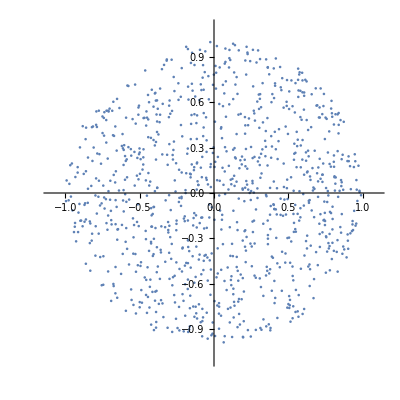

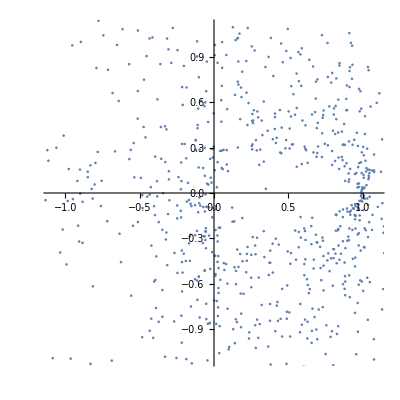

```mathematica
SeedRandom[29374];
μ={0,0};
Σ=IdentityMatrix[2];
n=1000;
pts=RandomPoint[Disk[],n];
λ=Total/@({#[[1]],#[[2]]*I}&/@pts);
ComplexListPlot[λ,PlotRange->{{-1.1,1.1},{-1.1,1.1}}]
D2=Table[(Re[λ1]-Re[λ2])^2+(Im[λ1]-Im[λ2])^2,{λ1,λ},{λ2,λ}];
SortedD2=Ordering/@D2;
λNN=Table[rand[[(#[[2]]&/@SortedD2)[[i]]]],{i,n}];
λNNN=Table[rand[[(#[[3]]&/@SortedD2)[[i]]]],{i,n}];
ratio=Table[zk[λ[[k]],λNN[[k]],λNNN[[k]]],{k,n}];ComplexListPlot[ratio,PlotRange->{{-1.1,1.1},{-1.1,1.1}}]
```

```mathematica
√(λ[[1]] Conjugate[λ[[1]]])
```

0.0195261+0. ⅈ

```mathematica
prueba=(RandomVariate[MultinormalDistribution[μ,Σ],{100}].{1.,1. I});
```

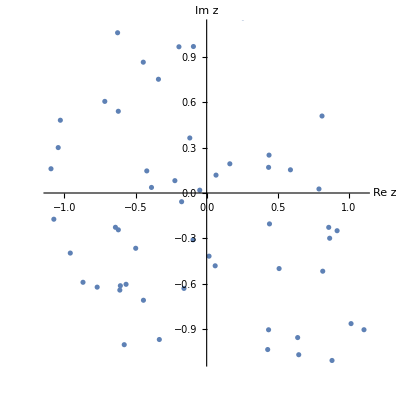

```mathematica
ComplexListPlot[prueba,PlotRange->{{-1.1,1.1},{-1.1,1.1}},AxesLabel->{"Re z","Im z"}]
```

```mathematica
RandomComplex[1+I,10]//Normalize
```

{0.319667+0.0483657 ⅈ,0.363424+0.387619 ⅈ,0.016911+0.0539527 ⅈ,0.146814+0.189912 ⅈ,0.259087+0.119855 ⅈ,0.321242+0.329076 ⅈ,0.17544+0.331264 ⅈ,0.0336855+0.085236 ⅈ,0.138178+0.0643749 ⅈ,0.195115+0.221654 ⅈ}

Distancia entre números: (en el plano complejo) √((x_2-x_1)^2+(y_2-y_1)^2)

```mathematica
D2=Table[(Re[λ1]-Re[λ2])^2+(Im[λ1]-Im[λ2])^2,{λ1,λ},{λ2,λ}];
```

```mathematica
(#[[2]]&/@(Ordering/@D2))
```

{7,6,4,3,6,2,1,10,7,8}

```mathematica
SortedD2=Ordering/@D2;
λNN=Table[rand[[(#[[2]]&/@SortedD2)[[i]]]],{i,n}];
λNNN=Table[rand[[(#[[3]]&/@SortedD2)[[i]]]],{i,n}];
```

```mathematica
ratio=Table[zk[λ[[k]],λNN[[k]],λNNN[[k]]],{k,n}];
```

{0.367734-0.0495201 ⅈ,0.463465-0.0575111 ⅈ,-0.293021-0.552838 ⅈ,-0.286564+0.550078 ⅈ,0.536535+0.0575111 ⅈ,-0.842642+0.197513 ⅈ,-0.571969+0.123119 ⅈ,0.0090958-0.00417003 ⅈ,0.632266+0.0495201 ⅈ,-0.00916142+0.00424687 ⅈ}

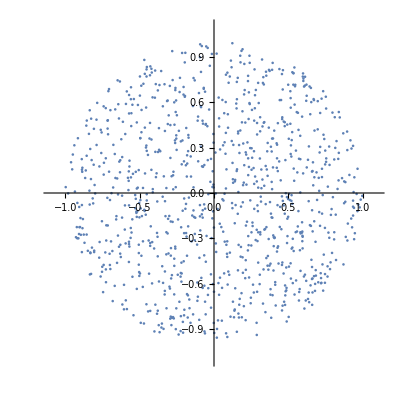

```mathematica
ComplexListPlot[ptas,PlotRange->{{-1.1,1.1},{-1.1,1.1}}]
```

```mathematica
pts=RandomPoint[Disk[],1000];
ptas=Total/@({#[[1]],#[[2]]*I}&/@pts);
```

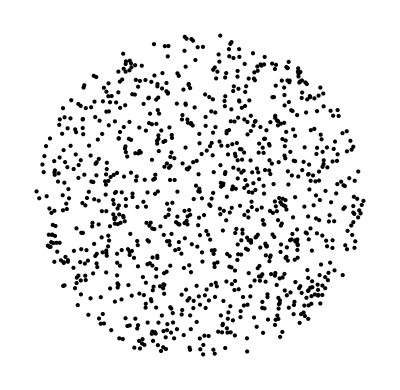

```mathematica
Graphics[{PointSize[Tiny],Point[pts]}]
```